### Start choosing the example:

```mathematica
t=23;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations["uvars"]
```

<|{1,1->2}→u37,{2,2->3}→u38,{3,3->1}→u39,{3,3->ex12}→u40,{en11,en11->1}→u41,{2,1->2}→u42,{3,2->3}→u43,{1,3->1}→u44,{ex12,3->ex12}→u45,{1,en11->1}→u46|>

```mathematica
MFGEquations["jvars"]
```

<|{2,1->2}→j13,{3,2->3}→j14,{1,3->1}→j15,{ex12,3->ex12}→j16,{1,en11->1}→j17,{1,1->2}→j18,{2,2->3}→j19,{3,3->1}→j20,{3,3->ex12}→j21,{en11,en11->1}→j22|>

```mathematica
MFGEquations["BoundaryRules"]
```

{j17→I1,u45→U1}

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1, U1->2,S1->0,S2->0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.109373,Null}

```mathematica
v0=MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j85→1+0-2/3,j86→1+0-2/3,j87→0,j88→1,j89→1,j90→2/3-2/3,j91→2/3-2/3,j92→2/3,j93→0,j94→0,jt100→2/3,jt101→1+0-2/3,jt102→2/3-2/3,jt103→0,jt104→1-2/3,jt105→2/3-2/3,jt106→2/3,jt107→0,jt108→0,jt95→2/3-2/3,jt96→0,jt97→0,jt98→0,jt99→1-2/3,u109→8/3,u110→7/3,u111→2,u112→2,u113→8/3,u114→-1-0+2/3+8/3,u115→-1-0+2/3+7/3,u116→-0+2/3+2,u117→2,u118→8/3|>

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

#### Non-linear case

```mathematica
alpha = 0;
beta = 0;
A = 0.2;
Parameters["alpha"] = alpha;
Parameters["beta"]=beta;
Parameters
```

<|alpha→0,beta→0,g[m]→Log,W[x,A]→Function[{x,a},a Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$83371[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$83371[x$]-g$83371[m$]]|>

```mathematica
MFGEquations["Nrhs"]
```

{j85-j90+Intg[j85-j90],j86-j91+Intg[j86-j91],j87-j92+Intg[j87-j92]}

```mathematica
FR=FixedReduceX1[MFGEquations]@ MFGEquations["criticalreduced1"][[2]]//KeySort
```

0.00849074

<|j409→0.31545,j410→0.31545,j411→0,j412→1,j413→1,j414→0,j415→0,j416→1-0.31545+0+0,j417→0,j418→0,jt419→0,jt420→0,jt421→0,jt422→0,jt423→0.31545-0,jt424→1-0.31545+0,jt425→0.31545,jt426→0,jt427→0,jt428→0.31545-0,jt429→0,jt430→1-0.31545+0,jt431→0,jt432→0,u433→2.54378,u434→2.27189,u435→2.,u436→2,u437→2.54378,u438→0.0435579-1. 0.31545+1. 0+1. 2.54378,u439→0.0435579-1. 0.31545+1. 0+1. 2.27189,u440→0.859235-1. 0.31545+1. 0+1. 2.,u441→2,u442→2.54378|>

```mathematica
FFR=FixedPoint[FixedReduceX1[MFGEquations], MFGEquations["criticalreduced1"][[2]], 14, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

0.00849074

0.00219461

0.000562875

0.00014407

0.0000368557

9.42707×10^-6

2.4112×10^-6

6.16719×10^-7

1.57739×10^-7

4.03451×10^-8

1.03191×10^-8

2.63934×10^-9

6.75067×10^-10

1.72663×10^-10

<|j409→0.309234,j410→0.309234,j411→0,j412→1,j413→1,j414→0,j415→0,j416→1-0.309234+0+0,j417→0,j418→0,jt419→0,jt420→0,jt421→0,jt422→0,jt423→0.309234-0,jt424→1-0.309234+0,jt425→0.309234,jt426→0,jt427→0,jt428→0.309234-0,jt429→0,jt430→1-0.309234+0,jt431→0,jt432→0,u433→2.54062,u434→2.27031,u435→2.,u436→2,u437→2.54062,u438→0.0389224-1. 0.309234+1. 0+1. 2.54062,u439→0.0389224-1. 0.309234+1. 0+1. 2.27031,u440→0.849858-1. 0.309234+1. 0+1. 2.,u441→2,u442→2.54062|>

```mathematica
FixedReduceX1[MFGEquations]@ %
```

2.35514×10^-16

<|j413→1,u441→2,j409→0.330656,j412→1,j414→0,j416→1-0.330656+0+0,j417→0,j418→0,jt419→0,jt420→0,jt421→0,jt422→0,jt423→0.330656-0,jt424→1-0.330656+0,jt425→0.330656,jt426→0,jt427→0,jt428→0.330656-0,jt429→0,jt430→1-0.330656+0,jt431→0,jt432→0,u436→2,u442→2.6517,u438→0.00480633-1. 0.330656+1. 0+1. 2.6517,u439→0.00480633-1. 0.330656+1. 0+1. 2.32585,u440→0.982357-1. 0.330656+1. 0+1. 2.,j410→0.330656,j411→0,j415→0,u433→2.6517,u434→2.32585,u435→2.,u437→2.6517|>

```mathematica
FixedSolverStepX1[MFGEquations]@ MFGEquations["criticalreduced1"][[2]]//KeySort
```

Possible multiple solutions 
{False,<|j89→1,u117→2,j85→1+0-2/3,j86→1+0-2/3,j88→1,j90→2/3-2/3,j91→2/3-2/3,j93→0,j94→0,jt101→1+0-2/3,jt102→2/3-2/3,jt103→0,jt104→1-2/3,jt105→2/3-2/3,jt106→2/3,jt107→0,jt108→0,jt95→2/3-2/3,jt96→0,jt97→0,jt98→0,jt99→1-2/3,u112→2,u114→-1-0+2/3+8/3,u115→-1-0+2/3+7/3,u116→-0+2/3+2,u118→8/3,j87→0,j92→2/3,jt100→2/3,u109→8/3,u110→7/3,u111→2,u113→8/3|>}

<|j89→1,u117→2,j85→1+0-2/3,j86→1+0-2/3,j88→1,j90→2/3-2/3,j91→2/3-2/3,j93→0,j94→0,jt101→1+0-2/3,jt102→2/3-2/3,jt103→0,jt104→1-2/3,jt105→2/3-2/3,jt106→2/3,jt107→0,jt108→0,jt95→2/3-2/3,jt96→0,jt97→0,jt98→0,jt99→1-2/3,u112→2,u114→-1-0+2/3+8/3,u115→-1-0+2/3+7/3,u116→-0+2/3+2,u118→8/3,j87→0,j92→2/3,jt100→2/3,u109→8/3,u110→7/3,u111→2,u113→8/3|>

{}

<|j85→1+0-2/3,j86→1+0-2/3,j87→0,j88→1,j89→1,j90→2/3-2/3,j91→2/3-2/3,j92→2/3,j93→0,j94→0,jt100→2/3,jt101→1+0-2/3,jt102→2/3-2/3,jt103→0,jt104→1-2/3,jt105→2/3-2/3,jt106→2/3,jt107→0,jt108→0,jt95→2/3-2/3,jt96→0,jt97→0,jt98→0,jt99→1-2/3,u109→8/3,u110→7/3,u111→2,u112→2,u113→8/3,u114→-1-0+2/3+8/3,u115→-1-0+2/3+7/3,u116→-0+2/3+2,u117→2,u118→8/3|>

```mathematica
FixedSolverStepX1[MFGEquations]@%//KeySort
```

Possible multiple solutions 
{False,<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>}

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

{}

<|j118→1/3,j119→1/3,j120→0,j121→1,j122→1,j123→0,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u142→8/3,u143→7/3,u144→2,u145→2,u146→8/3,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u150→2,u151→8/3|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]]//N,11, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

```mathematica
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol1
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol2
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol3n
```

0.153654

√(Abs[-u142+u147-Intg[j118-j123]]^2+Abs[-u143+u148-Intg[j119-j124]]^2+Abs[-u144+u149-Intg[j120-j125]]^2)

√(Abs[-u142+u147-Intg[j118-j123]]^2+Abs[-u143+u148-Intg[j119-j124]]^2+Abs[-u144+u149-Intg[j120-j125]]^2)

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

EqEliminartorX2: Count!

The system is False. Returning the inputs.

EqEliminartorX2: Count!

The system is False. Returning the inputs.

FixedX2: next step: j118-j123-u142+u147==j118-j123+Intg[j118-j123]&&j119-j124-u143+u148==1. j118-1. j123+Intg[1. j118-1. j123]&&j120-j125-u144+u149==-1.+1. j118-1. j123+Intg[-1.+1. j118-1. j123]

$Aborted

```mathematica
nsol3n=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest->(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

The system is False. Returning the inputs.

FixedX3: next step: j118-j123-u142+u147==j118-j123+Intg[j118-j123]&&j119-j124-u143+u148==1. j118-1. j123+Intg[1. j118-1. j123]&&j120-j125-u144+u149==-1.+1. j118-1. j123+Intg[-1.+1. j118-1. j123]

Throw::nocatch: Uncaught Throw[<|j122→1,u150→2,j119→1/3,j121→1,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u145→2,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u151→8/3,j118→1/3,j120→0,j123→0,u142→8/3,u143→7/3,u144→2,u146→8/3|>] returned to top level.

Hold[Throw[<|j122→1,u150→2,j119→1/3,j121→1,j124→0,j125→1-1/3+0+0,j126→0,j127→0,jt128→0,jt129→0,jt130→0,jt131→0,jt132→1/3-0,jt133→1-1/3+0,jt134→1/3,jt135→0,jt136→0,jt137→1/3-0,jt138→0,jt139→1-1/3+0,jt140→0,jt141→0,u145→2,u147→-1/3+0+8/3,u148→-1/3+0+7/3,u149→1-1/3+0+2,u151→8/3,j118→1/3,j120→0,j123→0,u142→8/3,u143→7/3,u144→2,u146→8/3|>]]

### What is this plot for?

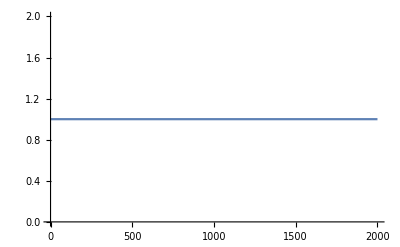
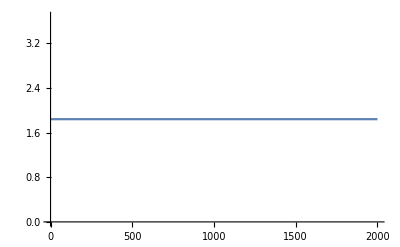
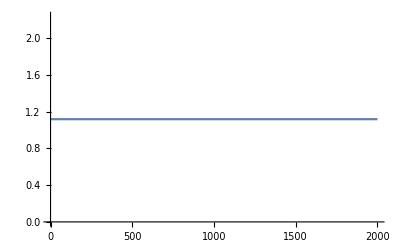
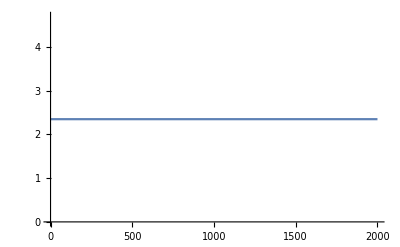
<|{2,1->2}→-Graphics-,{ex746,1->ex746}→-Graphics-,{3,2->3}→-Graphics-,{ex747,3->ex747}→-Graphics-,{2,en745->2}→-Graphics-,{1,1->2}→-Graphics-,{1,1->ex746}→-Graphics-,{2,2->3}→-Graphics-,{3,3->ex747}→-Graphics-,{en745,en745->2}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.